```mathematica
MakeEmpty[g_,vertices_]:=Block[{result=g},
Table[
If[EdgeQ[result,fromto],
result=EdgeDelete[result,fromto]
],
{fromto,Map[#[[1]]<->#[[2]]&,Subsets[vertices,{2}]]}
];
Graph[VertexList[result],EdgeList[result],VertexLabels->"Name"]
]
```

```mathematica
ZykovDecompositionEmpty[g_Graph,vertices_List]:=Block[{split,left, right,left2,right2,middle2,middle,sols,lefta,middlea,righta},
split= ConnectedComponents[VertexDelete[g,vertices]];
left=VertexDelete[g,split[[1]]];
right=VertexDelete[g,split[[2]]];
Print[{right,right}];
Interrupt[];
middle=VertexDelete[g,Select[DeleteDuplicates[Join[VertexList[left],VertexList[right]]],!MemberQ[vertices,#]&]];
left2=MakeEmpty[left,vertices];
right2=MakeEmpty[right,vertices];
middle2=MakeEmpty[middle,vertices];
sols=Reverse[Map[SymbolToSets,Sort[FindEmptyFormula[middle],CompareSymbols]]];
Print[sols];
Interrupt[];
Column[
{GraphWithChrom[Graph[EdgeList[g],GraphHighlight->EdgeList[CycleGr[vertices]],GraphHighlightStyle->"Thick", GraphLayout->"PlanarEmbedding",VertexLabels->"Name",ImageSize->400]],
TableForm[
Table[
middlea=ApplyToGraph[middle2,sol];
lefta=Graph[ApplyToGraph[left2,sol],GraphHighlight->EdgeList[middlea],GraphHighlightStyle->"Thick",ImageSize->200];
righta=Graph[ApplyToGraph[right2,sol],GraphHighlight->EdgeList[middlea],GraphHighlightStyle->"Thick",ImageSize->200];
With[{chrom=Simplify[(ChromaticPolynomial[lefta,x]*ChromaticPolynomial[righta,x]/ChromaticPolynomial[middlea,x])]},
{Rotate[Labeled[SetsToLabel[sol],(chrom/.x->4)],Pi/2],GraphWithChrom[lefta],GraphWithChrom[righta],GraphWithChrom[middlea],Rotate[Framed[Factor[chrom/(x(x-1))]],-Pi/2]}
],
{sol,sols}
]
]
}
]
]
```

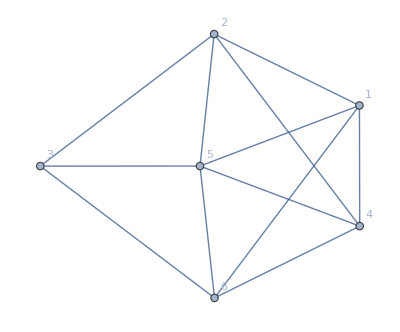

```mathematica
g=RandomGraph[{6,12}, VertexLabels->"Name"]
```

```mathematica
ZykovDecompositionEmpty[g,{1,4,5,6}]
```

Part::partw: Part 2 of {{2,3}} does not exist.